# Phase diagram and IBR graphs for the Prisoner’s Dilemma using the state space {CC} ,{DD, DC, CD}

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

Below we automatically set up the Bellman equations for all possible best-responses given an opponents strategy and self-consistently solve them to check whether there are allowed parameter combinations for which the best-response relation holds.

```mathematica
(*Converts n to a binary string of length l*)
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]

(*The ordering of the game. The first entry has to be a total order*)
ordering = {t>r>p>s};

(*Normalize by setting the outside parameters to 1 and 0.*)
outside = {First[ordering[[1]]/.{Greater ->List}],Last[ordering[[1]]/.{Greater ->List}]};
values = {outside[[1]]==1,outside[[2]]==0};

inside = DeleteCases[ordering[[1]] /.{Greater->List},Alternatives @@ outside];
changes = values/.{Equal->Rule};
restrictions= ordering/.changes;

(*Drawing restrictions*)
drestrictions = Flatten[{ordering,0<d<1, 0<epsilon<1}];

(*All restrictions*)
restrictions = Flatten[{drestrictions,values}];

(*All binary strategies: here the first entry corresponds to the action taken in the state: (CC) while the second entry corresponds to the action taken in the state (DD, DC, CD). A 0 indicates the defect action and a 1 indicates the cooperate action.*)
strats = Table[ Join[ConstantArray[0,2-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,3}];
```

```mathematica
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
(*Check every strat to see if it is a best-response*)
Do[{
strat = str[[j]];
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[strat[[1]]==0, Q100>Q101, Q100<Q101],
               If[strat[[2]]==0, Q110>Q111, Q110<Q111],
               If[input[[1]]==0, Q200>Q201, Q200<Q201],
               If[input[[2]]==0, Q210>Q211, Q210<Q211],
               drestrictions}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[Boole[Q200>Q201] ((1-epsilon/2)(p+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(t+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))+
                        Boole[Q200<Q201]((1-epsilon/2) (t+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(p+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))],
q2=  Simplify[Boole[Q200>Q201] ((1-epsilon/2)(s+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(r+d*((1-epsilon/2) Q100+epsilon/2 Q101)*Boole[Q100>Q101]+d*((1-epsilon/2) Q101+epsilon/2 Q100)*Boole[Q100<Q101]))+
                        Boole[Q200<Q201] ((1-epsilon/2)(r+d*((1-epsilon/2) Q100+epsilon/2 Q101)*Boole[Q100>Q101]+d*((1-epsilon/2) Q101+epsilon/2 Q100)*Boole[Q100<Q101])+epsilon/2(s+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))],
q3=  Simplify[Boole[Q210>Q211] ((1-epsilon/2)(p+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(t+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))+
                        Boole[Q210<Q211] ((1-epsilon/2)(t+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(p+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))],
q4=  Simplify[Boole[Q210>Q211] ((1-epsilon/2)(s+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111])+epsilon/2(r+d*((1-epsilon/2) Q100+epsilon/2 Q101)*Boole[Q100>Q101]+d*((1-epsilon/2) Q101+epsilon/2 Q100)*Boole[Q100<Q101]))+
                        Boole[Q210<Q211] ((1-epsilon/2)(r+d*((1-epsilon/2) Q100+epsilon/2 Q101)*Boole[Q100>Q101]+d*((1-epsilon/2) Q101+epsilon/2 Q100)*Boole[Q100<Q101])+epsilon/2(s+d*((1-epsilon/2) Q110+epsilon/2 Q111)*Boole[Q110>Q111]+d*((1-epsilon/2) Q111+epsilon/2 Q110)*Boole[Q110<Q111]))]
}];
sol1=Solve[{q1==Q100, q2==Q101, q3==Q110, q4==Q111},{Q100, Q101, Q110, Q111}];
conditions1=Simplify[Assuming[assumptions,{Simplify[If[strat[[1]]==0,sol1[[1]][[1]][[2]]>sol1[[1]][[2]][[2]],sol1[[1]][[1]][[2]]<sol1[[1]][[2]][[2]]]] ,If[strat[[2]]==0,sol1[[1]][[3]][[2]]>sol1[[1]][[4]][[2]], sol1[[1]][[3]][[2]]<sol1[[1]][[4]][[2]]]}]];
possiblebase=Simplify[conditions1[[1]]&&conditions1[[2]]];
possiblebase1=Assuming[{assumptions},Simplify[Reduce[possiblebase&&r<t&&r>p&&r>s&&t>p&&t>s&&p>s&&0<d&&1>d&&0<epsilon&&1>epsilon]]];
If[possiblebase1 , AppendTo[output,{FromDigits[i,2]+1->j,True}],,possible = Assuming[{assumptions},Simplify[conditions1[[1]]&&conditions1[[2]]]];
If[(possible === 0)==False , AppendTo[output,{FromDigits[i,2]+1->j,Simplify[possible]}]]]
},{j,1,4}];
output
];
```

```mathematica
result[strats[[2]], strats]
```

{{2→1,True}}

```mathematica
FullSimplify[sol1]
```

{{Q100→((-2+epsilon) (-2+d (2+(-2+epsilon) epsilon)) p+d epsilon (-((-2+epsilon) r)+epsilon (1+d-d epsilon) s)+(2 epsilon+d (4+epsilon (-6+(2+d (-1+epsilon)-epsilon) epsilon))) t)/(2 (-1+d) (-2+d (-1+epsilon) epsilon)),Q101→(2 epsilon (r-s)+4 s-d^2 (-2+epsilon) (-1+epsilon) epsilon (s-t)+d (-4 s+4 t+epsilon ((-2+epsilon)^2 p+4 s-6 t-epsilon (r+s+(-4+epsilon) t))))/(2 (-1+d) (-2+d (-1+epsilon) epsilon)),Q110→(epsilon ((2+2 d^2 (-1+epsilon)^2-d epsilon^2) p-d (-2+epsilon) r+d epsilon (1+d-d epsilon) s)-(-2+epsilon) (2+d (d (-1+epsilon)-epsilon) epsilon) t)/(2 (-1+d) (-2+d (-1+epsilon) epsilon)),Q111→(-2 (-2+epsilon) r+2 epsilon s+d (-((-2+epsilon) ((2+(-2+epsilon) epsilon) p+(-2+epsilon) r))-epsilon^2 s+(-2+epsilon)^2 epsilon t)+d^2 (-2+epsilon) (-1+epsilon) (2 (-1+epsilon) p+2 t-epsilon (s+t)))/(2 (-1+d) (-2+d (-1+epsilon) epsilon))}}

The code below produces a table showing the possible best-response relations and the conditions for their existence as well as a graph containing all possible best-response relationships.

0 | {0,0} | {{1→1,True}}
1 | {0,1} | {{2→1,True}}
2 | {1,0} | {{3→1,epsilon (p+r-s-t)+2 t+d (-1+epsilon) (2 (-1+epsilon) p+2 t-epsilon (s+t))>2 r&&(-2+epsilon) p+2 s+d epsilon^2 (s-t)+epsilon (r-(1+d) s+(-1+d) t)<0},{3→3,epsilon (p+r-s-t)+2 t+d (-1+epsilon) (2 (-1+epsilon) p+2 t-epsilon (s+t))<2 r&&(-2+2 d (-1+epsilon)^2+epsilon) p+epsilon (r+(-1+3 d) s+(-1+d) t)<2 (-1+d) s+d epsilon^2 (s+t)},{3→4,d epsilon^2 s+2 (d s+t)+epsilon (p+r+3 d t)<2 r+2 d t+d epsilon^2 t+epsilon (s+3 d s+t)&&2 (-1+d) s+d epsilon^2 (s+t)+epsilon (-r+s-3 d s+t-d t)<(-2+2 d (-1+epsilon)^2+epsilon) p}}
3 | {1,1} | {{4→1,True}}

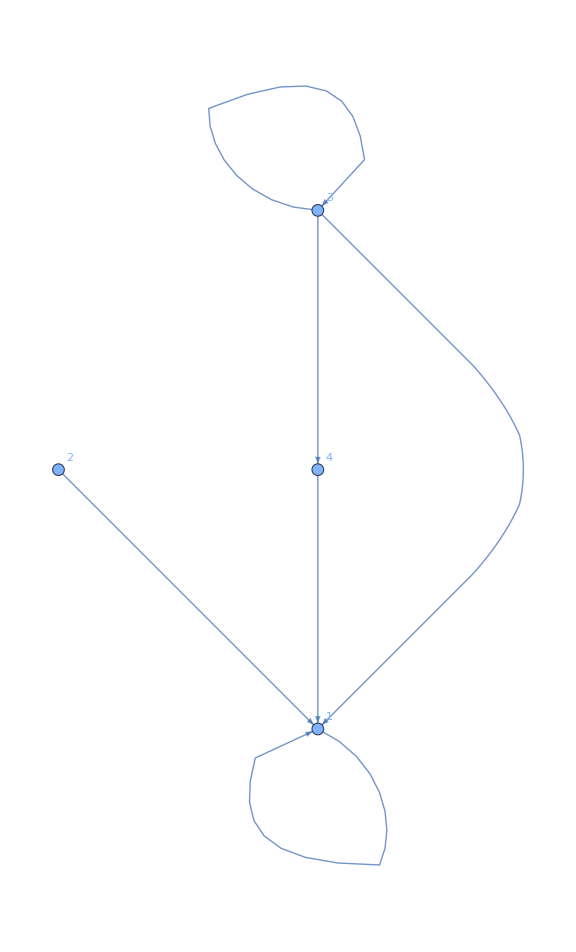

3

```mathematica
(*All best-responses*)
transitions = Table[result[strats[[i]],strats],{i,1,4}];

(*Grid of strategies and best-responses*)
grid = Table[{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]},{i,1,4}];
Grid[grid,Frame->All]

(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
labels = Flatten[Table[Table[transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Large]

(*Count the amount of possible graphs*)
Times @@ Table[Length[transitions[[i]]],{i,1,4}]
```

Below we rewrite the critical conditions. For the first one we have

```mathematica
{epsilon (p+r-s-t)+2 t+d (-1+epsilon) (2 (-1+epsilon) p+2 t-epsilon (s+t))>2 r&&(-2+epsilon) p+2 s+d epsilon^2 (s-t)+epsilon (r-(1+d) s+(-1+d) t)<0};
```

```mathematica
Solve[(-2+epsilon) p+2 s+d epsilon^2 (s-t)+epsilon (r-(1+d) s+(-1+d) t)==0, d]
```

{{d→(2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) epsilon (s-t))}}

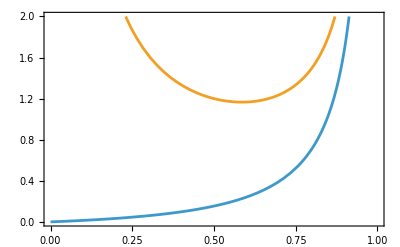

```mathematica
With[{t=1, s=0, r=0.9999, p=0.2},Plot[{(-epsilon p+2 r-epsilon r+epsilon s-2 t+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p-epsilon s+2 t-epsilon t)), (2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) epsilon (s-t))}, {epsilon, 0, 1}, PlotRange->{0, 2}, Frame->True]]
```

By plotting both of the conditions, we see that only the first is relevant. For the second condition, we have

```mathematica
epsilon (p+r-s-t)+2 t+d (-1+epsilon) (2 (-1+epsilon) p+2 t-epsilon (s+t))<2 r&&(-2+2 d (-1+epsilon)^2+epsilon) p+epsilon (r+(-1+3 d) s+(-1+d) t)<2 (-1+d) s+d epsilon^2 (s+t)
```

```mathematica
Solve[(-2+2 d (-1+epsilon)^2+epsilon) p+epsilon (r+(-1+3 d) s+(-1+d) t)==2 (-1+d) s+d epsilon^2 (s+t), d]
```

{{d→(2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p+2 s-epsilon s-epsilon t))}}

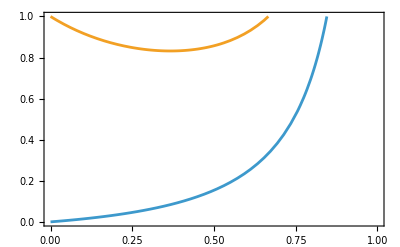

```mathematica
With[{t=1, s=0, r=0.9999, p=0.2},Plot[{(-epsilon p+2 r-epsilon r+epsilon s-2 t+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p-epsilon s+2 t-epsilon t)), (2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p+2 s-epsilon s-epsilon t))}, {epsilon, 0, 1}, PlotRange->{0, 1}, Frame->True]]
```

```mathematica
TeXForm[(2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p+2 s-epsilon s-epsilon t))]
```

\frac{-\epsilon  p-\epsilon  r+\epsilon  s+\epsilon  t+2 p-2 s}{(\epsilon -1) (2
   \epsilon  p-\epsilon  s-\epsilon  t-2 p+2 s)}

```mathematica
(-epsilon p+2 r-epsilon r+epsilon s-2 t+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p-epsilon s+2 t-epsilon t))-(-epsilon p+2 r-epsilon r+epsilon s-2 t+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p-epsilon s+2 t-epsilon t))
```

0

Here both of the conditions are relevant. For the third condition, we have

```mathematica
d epsilon^2 s+2 (d s+t)+epsilon (p+r+3 d t)<2 r+2 d t+d epsilon^2 t+epsilon (s+3 d s+t)&&2 (-1+d) s+d epsilon^2 (s+t)+epsilon (-r+s-3 d s+t-d t)<(-2+2 d (-1+epsilon)^2+epsilon) p
```

```mathematica
Solve[2 (-1+d) s+d epsilon^2 (s+t)+epsilon (-r+s-3 d s+t-d t)==(-2+2 d (-1+epsilon)^2+epsilon) p, d]
```

{{d→(2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p+2 s-epsilon s-epsilon t))}}

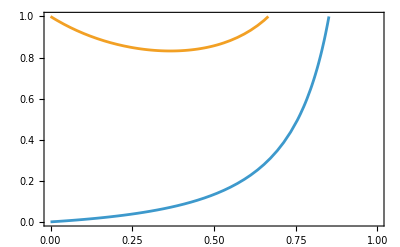

```mathematica
With[{t=1, s=0, r=0.9999, p=0.2},Plot[{(-epsilon p+2 r-epsilon r+epsilon s-2 t+epsilon t)/((2-3 epsilon+epsilon^2) (s-t)), (2 p-epsilon p-epsilon r-2 s+epsilon s+epsilon t)/((-1+epsilon) (-2 p+2 epsilon p+2 s-epsilon s-epsilon t))}, {epsilon, 0, 1}, PlotRange->{0, 1}, Frame->True]]
```

Here we see that only the top condition is relevant as the other is always satisfied.

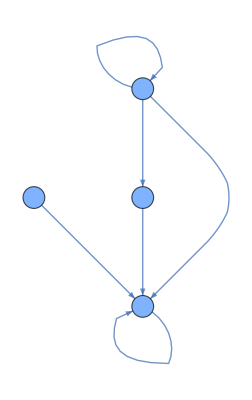

```mathematica
(*Plot the Maximal IBR graph containing all possible transitions*)
GraphPlot[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.2,  DirectedEdges->True, ImageSize->Full]
```

Next we check which best-response relationships can hold simultaneously. This splits the parameter space into regions where each region corresponds to one IBR graph. Here the strategy GT is labeled by a 3 and the AD strategy is labeled by a 1. A self-loop at a node implies that it is an equilibrium.

```mathematica
(*Find the actual possible graphs by adding a restriction one at the time if it does not yield an empty region*)

(*Here will will get all graphs and their regions*)
(*We will initialise with the transitions from 0 and their regions*)
possible = Table[{transitions[[1]][[j]][[1]],transitions[[1]][[j]][[2]]},{j,1,Length[transitions[[1]]]}];

Do[
(*Updated possible after adding the next round of transitions*)
next = {};
Do[
Do[
(*Add a new transition to possible[[k]]*)
function = Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],transitions[[i]][[j]][[2]]]]];
(*If the new region is non empty, add possible[[k]] with the new transition to next*)
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],transitions[[i]][[j]][[1]]}],Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
,{j,1,Length[transitions[[i]]]}];
possible = next;
,{i,2,4}];        

(*Add the restrictions*)
Graphs = Table[{possible[[i]][[1]],FullSimplify[possible[[i]][[2]]&&( And @@ drestrictions)]},{i,1,Length[possible]}];

(*Delete regions which will now become empty*)
Graphs = DeleteCases[Graphs,{_,False}];

Grid[Table[{i,Graphs[[i]][[1]],Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]

edgeslist = Graphs[[All,1]];
todraw = Graphs[[All,2]];
```

1 | {1→1,2→1,3→1,4→1} | epsilon (-1+d-d epsilon+p+r)<2 p&&2+d (-1+epsilon) (2-epsilon+2 (-1+epsilon) p)+epsilon (-1+p+r)>2 r&&t>r>p>s&&0<d<1&&0<epsilon<1
2 | {1→1,2→1,3→3,4→1} | (-2+2 d (-1+epsilon)^2+epsilon) p+epsilon (-1+d+r)<d epsilon^2&&2+d (-1+epsilon) (2-epsilon+2 (-1+epsilon) p)+epsilon (-1+p+r)<2 r&&t>r>p>s&&0<d<1&&0<epsilon<1
3 | {1→1,2→1,3→4,4→1} | epsilon (1+d (-1+epsilon)-r)<(-2+2 d (-1+epsilon)^2+epsilon) p&&2+epsilon (3 d+p+r)<epsilon+d (2+epsilon^2)+2 r&&t>r>p>s&&0<d<1&&0<epsilon<1

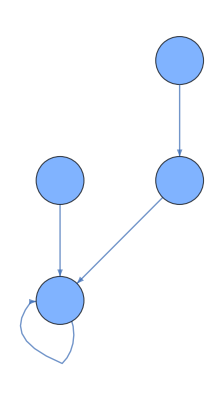

```mathematica
Graph[Graphs[[3]][[1]], VertexLabels->Placed[Automatic,Center],VertexSize->.4,GraphLayout->"LayeredDigraphEmbedding"]
```

The next cell produces the phase diagram where each region corresponds to a unique IBR graph. Here the numbering of of the regions corresponds to the numbering of the graphs in the next cell. The only IBR graph in which (GT, GT) is an equilibrium is the second IBR graph corresponding to the yellow region in the phase diagram. Therefore, the parameters have to satisfy the conditions to be in the yellow region for cooperation to be possible.

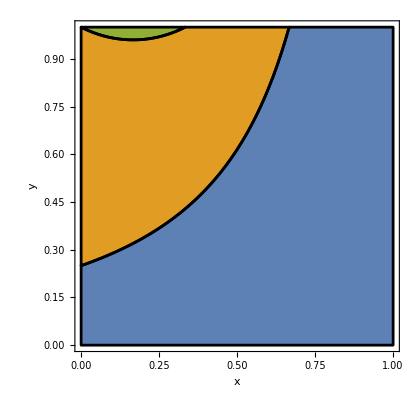

```mathematica
formulas = ReplaceAll[todraw, {d->y,epsilon->x,r->0.8,p->0.2, t->1, s->0}];
TwoActionPDsimilarityphaser8p2=RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotStyle->{ColorData[97][1], ColorData[97][2], ColorData[97][3], ColorData[97][4], ColorData[97][5], ColorData[97][6], ColorData[97][7], ColorData[97][8], ColorData[97][9], ColorData[97][15], ColorData[1][1], ColorData[1][2]},BoundaryStyle->Black,PlotLegends->Placed[MaTeX/@{"G_{1}","G_{2}", "G_{3}"}, {0.15, 0.65}],PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\epsilon","\\gamma"}, MaxRecursion->5]
```

```mathematica
N[(3/4-1/4)/(1/4)]
```

2.

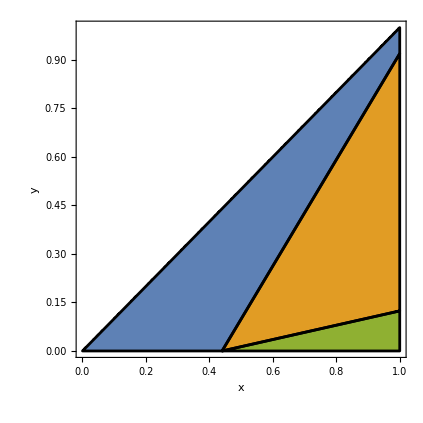

```mathematica
formulas = ReplaceAll[todraw, {d->0.7,epsilon->0.2,r->x,p->y, t->1, s->0}];
TwoActionPDsimilarityphased7e2=RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotStyle->{ColorData[97][1], ColorData[97][2], ColorData[97][3], ColorData[97][4], ColorData[97][5], ColorData[97][6], ColorData[97][7], ColorData[97][8], ColorData[97][9], ColorData[97][15], ColorData[1][1], ColorData[1][2]},BoundaryStyle->Black,PlotLegends->Placed[MaTeX/@{"G_{1}","G_{2}", "G_{3}"}, {0.15, 0.65}],PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"R","P"}, MaxRecursion->5]
```

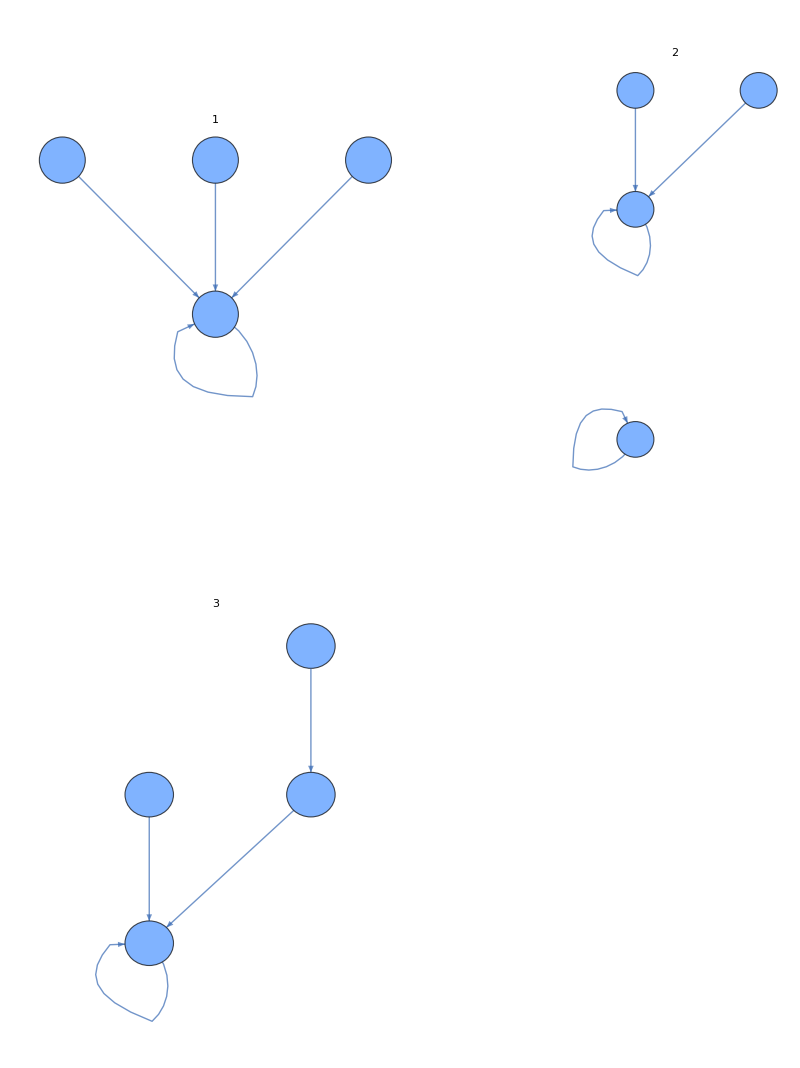

```mathematica
(*Make a grid with the different graphs (as square as possible)*)
grid = ArrayReshape[Table[Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexSize->.3,  DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}],{Ceiling[Sqrt[Length[Graphs]]],Ceiling[Sqrt[Length[Graphs]]]}];

(*Convert the zeroes on the empty spaces in the grid to empty graphics*)
Do[Do[If[grid[[i]][[j]]==0, grid[[i]][[j]] = Graphics[{}]],{j,1,Length[grid[[i]]]}],{i,1,Length[grid]}]

(*Delete the empty rows*)
Do[If[grid[[i]] == ConstantArray[Graphics[{}],Length[grid[[i]]]],grid = grid[[1;;i-1]]; Break[]],{i,1,Length[grid]}]

(*Draw the grid*)
GraphicsGrid[grid,Frame->All,ImageSize->Full]
```

## Exporting

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
format=".pdf";
di=72; bl=1;cs=3.5;
```

```mathematica
Export["TwoActionPDsimilarityphaser8p2"<>format,TwoActionPDsimilarityphaser8p2]
```

TwoActionPDsimilarityphaser8p2.pdf